# Paper Exports

Kathrin Laxhuber, 2019

## Init

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Package Imports

```mathematica
<<"NullclinePlots`"
```

```mathematica
<<"CurvesGraphics6`"
```

```mathematica
<<MaTeX`
```

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:/Program Files/MiKTeX 2.9/miktex/bin/x64/pdflatex.exe","Ghostscript"->"C:/Program Files/gs/gs9.26/bin/gswin64c.exe"];
```

### Plot Options

```mathematica
plotOptionsBasic={Frame->True,FrameStyle->BlackFrame};
```

```mathematica
texStyle={FontFamily->"Times",FontSize->11};
plotSizesLaTeX=<|"Normal"->350,"Two"->250,"Three"->180|>;
```

### System ODE’s

3d equations for 3D plot:

```mathematica
dmdt3d[params_]:=params[["ρ_m"]](
(params[["XapR"]] (1+x/params[["K_χA"]])^2/((1+x/params[["K_χA"]])^2+Exp[params[["ϵ_x"]]] (1+x/params[["K_χI"]])^2))^2
Exp[params[["ϵ_coop"]]]
)/(
1+
2 (params[["XapR"]] (1+x/params[["K_χA"]])^2/((1+x/params[["K_χA"]])^2+Exp[params[["ϵ_x"]]] (1+x/params[["K_χI"]])^2))+
(params[["XapR"]] (1+x/params[["K_χA"]])^2/((1+x/params[["K_χA"]])^2+Exp[params[["ϵ_x"]]] (1+x/params[["K_χI"]])^2))^2
Exp[params[["ϵ_coop"]]]
)-params[["γ"]]m;
dpdt3d[params_]:=params[["ρ_p"]] m - p;
dxdt3d[params_]:=(params[["k_(β, i)"]] (params[["c"]])/(params[["K_(β, i)"]]+params[["c"]])-params[["k_(β, e)"]] (x)/(params[["K_(β, e)"]]+x)-params[["k_α"]] (x)/(1+x)) p+params[["k_η"]](params[["c"]]-params[["ξ"]] x);
```

2d equations as functions for 2d plots:

```mathematica
ActiveXapR[x_,XapR_,ϵx_,KA_,KI_]:=XapR (1+x/KA)^2/((1+x/KA)^2+Exp[ϵx] (1+x/KI)^2);

dpdt[p_,x_,params_]:=params[["ρ"]] (
ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]^2
Exp[params[["ϵ_coop"]]]
)/(
1+
2 ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]+
ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]^2
Exp[params[["ϵ_coop"]]]
)-p;

dxdt[p_,x_,params_]:= (params[["k_(β, i)"]] (params[["c"]])/(params[["K_(β, i)"]]+params[["c"]])-params[["k_(β, e)"]] (x)/(params[["K_(β, e)"]]+x)-params[["k_α"]] (x)/(1+x)) p+params[["k_η"]](params[["c"]]-params[["ξ"]] x);
```

### Rasterization

```mathematica
MakeTransparent[obj_]:=Module[{res=obj},Switch[obj[[0]],
Graphics,res[[1]]=Join[{Opacity[0]},res[[1]]],
String,Style[res,Opacity[0]],
StringForm,Style[res,Opacity[0]]
];
res
]
```

```mathematica
Options[Rasterize3DPlot]={Overlay->{},HiddenVertex->Automatic};
Rasterize3DPlot[g_,pre_,res_,OptionsPattern[]]:=Module[{opts,axes,invisible,content,boxbg,boxfg,vertices,viewdist,hidden,edges,out},
axes=Show[g,Boxed->False];
opts=AbsoluteOptions[axes];
axes[[-1]]=opts;
invisible=Show[axes,pre,AxesStyle->Opacity[0],AxesLabel->MakeTransparent/@(AxesLabel/.opts)];
content=Rasterize[invisible,RasterSize->res,ImageSize->(ImageSize/.opts),Background->None];
axes[[1]]={};
invisible[[1]]={};
vertices=Tuples[PlotRange/.AbsoluteOptions[g]];
viewdist=Norm[#-(ViewPoint/.opts)]&/@vertices;
hidden=If[OptionValue[HiddenVertex]===Automatic,vertices[[FirstPosition[viewdist,Max[viewdist]][[1]]]],OptionValue[HiddenVertex]];
edges=Select[Subsets[vertices,{2}],Count[Differences[#][[1]],x_?(#≠0&)]==1&];
boxbg=Graphics3D[Join[{BoxStyle/.opts},Line/@Select[edges,MemberQ[#,hidden]&]],Boxed->False];
boxfg=Graphics3D[Join[{BoxStyle/.opts},Line/@Select[edges,!MemberQ[#,hidden]&]],Boxed->False];
out=Show[invisible,boxbg,Epilog->Inset[Show[axes,boxfg,OptionValue[Overlay],Prolog->Inset[content,ImageScaled[{0,0 0.01}],ImageScaled[{0,0}],ImageScaled[1]]]],ImageSize->(ImageSize/.opts),ImageMargins->3];
ImportString[ExportString[Graphics[Inset[out],ImageSize->ImageDimensions[out],ImageMargins->2,AspectRatio->Full],"PDF",Background->None]][[1]]
]
```

### Other Definitions

```mathematica
inch = 72;
```

## Various

### Induction Curve

```mathematica
fInd[eps_,KI_,KA_]:=(1+(2 10^(x/3))/KA)^2/((1+(2 10^(x/3))/KA)^2+Exp[eps](1+(2 10^(x/3))/KI)^2)
```

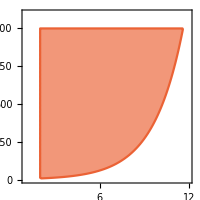

```mathematica
RegionParams=Show[RegionPlot[True,{Ex,1,12},{KIA,0,1.1 10^3},ImageSize->200,PlotStyle->White,BoundaryStyle->White, FrameLabel->{MaTeX["\\Delta \\epsilon_{\\mathrm{x}}",Magnification->0.8],MaTeX["K_{\\mathrm{IA}}",Magnification->0.8]},ImageSize->200,BaseStyle->{FontFamily->"Times",FontSize->8,FontColor->Black}],RegionPlot[KIA>3 Exp[Ex/2]&&Ex>2&&KIA<10^3,{Ex,1,12},{KIA,0,1.1 10^3},FrameLabel->{MaTeX["\\Delta \\epsilon_{\\mathrm{x}}",Magnification->0.8],MaTeX["K_{\\mathrm{IA}}",Magnification->0.8]},ImageSize->200,BaseStyle->{FontFamily->"Times",FontSize->8,FontColor->Black},Background->None,PlotStyle->Lighter[ColorData[97,4]],BoundaryStyle->ColorData[97,4]]]
```

```mathematica
IndCurve=Plot[
{fInd[3,10^4,10^(2)],fInd[3,10^5,10^(2)],fInd[3,10^3,10^(2)],
fInd[5,10^4,10^(2)],fInd[5,10^5,10^(2)],fInd[5,10^3,10^(2)],
fInd[7,10^4,10^(2)],fInd[7,10^5,10^(2)],fInd[7,10^3,10^(2)]},
{x,4,16},
Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},PlotStyle->{ColorData[97,1],{Lighter[ColorData[97,1]],Thin},{Lighter[ColorData[97,1]],Thin},ColorData[97,2],{Lighter[ColorData[97,2]],Thin},{Lighter[ColorData[97,2]],Thin},ColorData[97,3],{Lighter[ColorData[97,3]],Thin},{Lighter[ColorData[97,3]],Thin}},
PlotLegends->Placed[{MaTeX["\\Delta \\epsilon_{\\mathrm{x}}=3",Magnification->1],None,None,MaTeX["\\Delta \\epsilon_{\\mathrm{x}}=5",Magnification->1],None,None,MaTeX["\\Delta \\epsilon_{\\mathrm{x}}=7",Magnification->1],None,None},{0.14,0.78}],
PlotRange->Full, Frame->True, FrameLabel->{MaTeX["\\mathrm{Log([x]/nM)}",Magnification->1],MaTeX["p_{\\mathrm{active}}",Magnification->1]},ImageSize->370,PlotStyle->{FontFamily->"Times",FontSize->11},Axes->False,FrameTicks->True,Epilog->Inset[RegionParams,{13.4,0.32},Automatic,5]]
```

$Aborted

```mathematica
Export[FileNameJoin[{"Exports","FigSI3.pdf"}],IndCurve];
```

## Phase Portraits

```mathematica
params3d=<|"ρ_m"->10^(-3),"ρ_p"->10^2,"γ"->10^1,"XapR"->10^(0),"c"->1.3 10^(1),"k_(β, i)"->5 10^4,"k_(β, e)"->10^3,"k_α"->10^2,"k_η"->5 10^(-1),"K_(β, i)"->10^1,"K_(β, e)"->10^2,"K_χA"->10^2,"K_χI"->10^4,"ξ"-> 0.8,"ϵ_x"->5,"ϵ_coop"->5|>;
```

```mathematica
params2d=<|"ρ"->10^(-2),"XapR"->10^(0),"c"->13,"k_(β, i)"->5 10^4,"k_(β, e)"->10^3,"k_α"->10^2,"k_η"->5 10^(-1),"K_(β, i)"->10^1,"K_(β, e)"->10^2,"K_χA"->10^2,"K_χI"->10^4,"ξ"-> 0.8,"ϵ_x"->5,"ϵ_coop"->5|>;
```

### 3D Phase Portraits

```mathematica
Streamlines=PhasePlot[{dmdt3d[params3d],dpdt3d[params3d],dxdt3d[params3d]},{m,0,10^(-4)},{p,0,0.0095},{x,0,700},{0,0.6},GridPoints->{2,5,5},PlotStyle->{Gray,Opacity[0.6],Thickness[0.007]},BoxRatios->{1,1,1},Axes->True,AxesLabel->{MaTeX["\\mathrm{[m]_a}",Magnification->1.1],MaTeX["\\mathrm{[p]_a}",Magnification->1.1],MaTeX["\\mathrm{[x]_a}",Magnification->1.1]},HeadScaling3D->0.1,ImageSize->200];

Planes=ContourPlot3D[{dxdt3d[params3d]==0,dpdt3d[params3d]==0,dmdt3d[params3d]==0},{m,0,10^(-4)},{p,0,0.0095},{x,0,700},PlotLegends->{MaTeX["\\frac{\\mathrm{d}\\mathrm{[x]_a}}{\\mathrm{d}t}=0",Magnification->1.1],MaTeX["\\frac{\\mathrm{d}\\mathrm{[p]_a}}{\\mathrm{d}t}=0",Magnification->1.1],MaTeX["\\frac{\\mathrm{d}\\mathrm{[m]_a}}{\\mathrm{d}t}=0",Magnification->1.1]},ImageSize->200];

PhasePortrait3D=Show[Streamlines,Planes,ViewPoint->{0.415358378,-2.806840875,1.8436707189},ImageSize->200,Background->Transparent,BaseStyle->{FontFamily->"Times"}]
```

-Graphics3D-

### 2D Phase Portraits

#### General

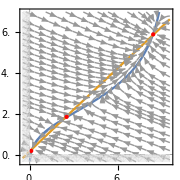

```mathematica
General2D=NullclinePlotSystem[{dpdt,dxdt},params2d,FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.000475,0.0095} ,{-35,700}},FontStyle->"LaTeX",PlotSize->"Three",
Epilog->{{Red,PointSize@Medium,Point[{0.0001,18}]},{Red,PointSize@Medium,Point[{0.00837,590}]},{Red,PointSize@Medium,Point[{0.0025,185}]},
Inset[MaTeX["{\\color{red} 1}",Magnification->1.2,"Preamble"->{"\\usepackage{color}"}],ImageScaled[{0.27,0.22}],ImageScaled[{0,0}]],Inset[MaTeX["{\\color{red} 2}",Magnification->1.2,"Preamble"->{"\\usepackage{color}"}],ImageScaled[{0.45,0.35}],ImageScaled[{0,0}]],Inset[MaTeX["{\\color{red} 3}",Magnification->1.2,"Preamble"->{"\\usepackage{color}"}],ImageScaled[{0.82,0.82}],ImageScaled[{0,0}]]}]
```

```mathematica
resolution=1500 (* pixels *);
legendres=100 (* pixels *);
subfigsize=200(* pt *);
FIGWIDTH=500(* pt *);
approxfigheight=220(* pt *);
figPortrait=Graphics[{
(* 3D *)
Inset[Rasterize3DPlot[Show[PhasePortrait3D[[1]],ImageSize->subfigsize],{},resolution,HiddenVertex->{0.,0.0095,0.}],ImageScaled[{0,0}],ImageScaled[{0,0}]],
Inset[SwatchLegend[PhasePortrait3D[[2,1,1,;;,2]],PhasePortrait3D[[2,1,2]],LegendMarkers->(ImportString[ExportString[Rasterize[#,RasterSize->legendres],"PDF"],"PDF"][[1]]&/@(Graphics3D[{##,Sphere[List[0,0,0]]},Rule[ViewPoint,List[0,0,DirectedInfinity[1]]],Rule[PlotRange,List[List[-0.7,0.7],List[-0.7,0.7],All]],Rule[ImagePadding,0]]&/@PhasePortrait3D[[2,1,1]]))],ImageScaled[{0.42,0.5}],ImageScaled[{0,0.5}]],
(* 2D *)
Inset[Show[General2D,ImageSize->subfigsize],ImageScaled[{1,0}],ImageScaled[{1,0}]],
(* labels *)
Inset[MaTeX["\\mathrm{(A)}",Magnification->1.1],ImageScaled[{0,1}],ImageScaled[{0,1}]],
Inset[MaTeX["\\mathrm{(B)}",Magnification->1.1],ImageScaled[{0.58,1}],ImageScaled[{0,1}]]
},PlotRange->{All,{-1,1}approxfigheight/FIGWIDTH},ImageSize->{FIGWIDTH,Automatic}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","Bistability.pdf"}],figPortrait];
```

```mathematica
Bistabilityresize=Show[ImportString[ExportString[figPortrait,"PDF"],"PDF"],ImageSize->5.2*inch];
```

```mathematica
Export[FileNameJoin[{"Exports","Bistability.eps"}],Bistabilityresize];
```

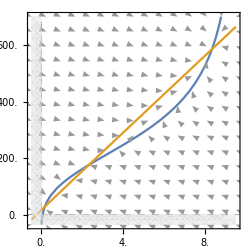

```mathematica
Vector2D=VectorNullclinePlotSystem[{dpdt,dxdt},params2d,FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.000475,0.0095} ,{-35,700}},FontStyle->"LaTeX",PlotSize->"Two",VectorScale->{0.00005,Scaled[0.5],#5&}]
```

```mathematica
Export[FileNameJoin[{"Exports","FigSI4.pdf"}],Vector2D];
```

#### Varying C

```mathematica
LowC=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"c"->7|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.0005,0.01} ,{-50,1000}},FontStyle->"LaTeX",PlotSize->"Two",Epilog->{Red,PointSize@Medium,Point[{0.00018,18}]}];
```

```mathematica
HighC=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"c"->40|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.0005,0.01} ,{-50,1000}},FontStyle->"LaTeX",PlotSize->"Two",Epilog->{Red,PointSize@Medium,Point[{0.00925,950}]}];
```

```mathematica
VaryingC=Graphics[{Inset[LowC,ImageScaled[{0.01,0}],ImageScaled[{0,0}]],Inset[HighC,ImageScaled[{1,0}],ImageScaled[{1,0}]],Inset[MaTeX["\\mathrm{(A)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],Inset[MaTeX["\\mathrm{(B)}",Magnification->1.2],ImageScaled[{0.525,1}],ImageScaled[{0,1}]],
Inset[MaTeX["\\mathrm{Low~[c]_a}",Magnification->1.2],ImageScaled[{0.12,0.89}],ImageScaled[{0,1}],Background->White],Inset[MaTeX["\\mathrm{High~[c]_a}",Magnification->1.2],ImageScaled[{0.645,0.89}],ImageScaled[{0,1}],Background->White],
Inset[MaTeX["{\\color{red} 1}",Magnification->1.2,"Preamble"->{"\\usepackage{color}"}],ImageScaled[{0.125,0.18}],ImageScaled[{0,0}]],Inset[MaTeX["{\\color{red} 3}",Magnification->1.2,"Preamble"->{"\\usepackage{color}"}],ImageScaled[{0.932,0.82}],ImageScaled[{0,0}]]},
PlotRange->{All,{-1,1}280/540},ImageSize->{540,Automatic}]
```

-Graphics-

```mathematica
VaryingCLegended=Legended[VaryingC,Placed[LineLegend[{ColorData[97,1],ColorData[97,2]},MaTeX[#,"FontSize"->14]&/@{"\\frac{\\mathrm{d}\\mathrm{[x]_a}}{\\mathrm{d}t}=0","\\frac{\\mathrm{d}\\mathrm{[p]_a}}{\\mathrm{d}t}=0"},LegendLayout->{"Row",1},Spacings->{1,4,-1},LegendMarkerSize->30,LegendMargins->5],Below]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","VaryingC.pdf"}],VaryingCLegended];
```

```mathematica
VaryingCresize=Show[ImportString[ExportString[VaryingCLegended,"PDF"],"PDF"],ImageSize->5.2*inch];
```

```mathematica
Export[FileNameJoin[{"Exports","VaryingC.eps"}],VaryingCresize];
```

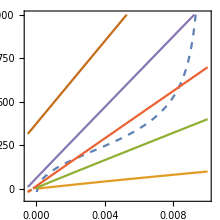

```mathematica
CFamily=ContourPlot[Evaluate@Flatten[{dpdt[p,x,params2d]==0,Evaluate@Table[{dxdt[p,x,params]==0},{params,{Append[params2d,<|"c"->1|>],Append[params2d,<|"c"->5|>],Append[params2d,<|"c"->13|>],Append[params2d,<|"c"->50|>],Append[params2d,<|"c"->300|>]}}]}],{p,-0.0005,0.01} ,{x,-50,1000},ContourStyle->{{Thick,Dashed},Automatic,Automatic,Automatic,Automatic,Automatic},Frame->True,FrameLabel->MaTeX@{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotLegends->MaTeX@{"\\mathrm{[c]_a} \\in \\mathbb{R}_+","\\mathrm{[c]_a}=1","\\mathrm{[c]_a}=5","\\mathrm{[c]_a}=13","\\mathrm{[c]_a}=50","\\mathrm{[c]_a}=300"},ImageSize->220]
```

```mathematica
Export[FileNameJoin[{"Exports","FigSI5.pdf"}],CFamily];
```

#### No XapA / XapB

```mathematica
NoXapA=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"k_α"->0|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.000475,0.0095} ,{-35,700}},FontStyle->"LaTeX",PlotSize->"Two",Epilog->{{Red,PointSize@Medium,Point[{0.00018,30}]},{Red,PointSize@Medium,Point[{0.0023,175}]},{Red,PointSize@Medium,Point[{0.00835,590}]}}];
```

```mathematica
NoXapB=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"k_(β, i)"->0,"k_(β, e)"->0|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.000475,0.0095} ,{-35,700}},FontStyle->"LaTeX",PlotSize->"Two",Epilog->{Red,PointSize@Medium,Point[{0.00014,17}]}];
```

```mathematica
XapAB=Graphics[{Inset[NoXapA,ImageScaled[{0.01,0}],ImageScaled[{0,0}]],Inset[NoXapB,ImageScaled[{1,0}],ImageScaled[{1,0}]],Inset[MaTeX["\\mathrm{(A)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],Inset[MaTeX["\\mathrm{(B)}",Magnification->1.2],ImageScaled[{0.525,1}],ImageScaled[{0,1}]],
Inset[MaTeX["\\mathrm{No~XapA}",Magnification->1.2],ImageScaled[{0.12,0.89}],ImageScaled[{0,1}],Background->White],Inset[MaTeX["\\mathrm{No~XapB}",Magnification->1.2],ImageScaled[{0.645,0.89}],ImageScaled[{0,1}],Background->White]},PlotRange->{All,{-1,1}280/540},ImageSize->{540,Automatic}]
```

-Graphics-

```mathematica
XapABLegended=Legended[XapAB,Placed[LineLegend[{ColorData[97,1],ColorData[97,2]},MaTeX[#,"FontSize"->14]&/@{"\\frac{\\mathrm{d}\\mathrm{[x]_a}}{\\mathrm{d}t}=0","\\frac{\\mathrm{d}\\mathrm{[p]_a}}{\\mathrm{d}t}=0"},LegendLayout->{"Row",1},Spacings->{1,4,-1},LegendMarkerSize->30,LegendMargins->5],Below]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","XapAB.pdf"}],XapABLegended];
```

```mathematica
XapABresize=Show[ImportString[ExportString[XapABLegended,"PDF"],"PDF"],ImageSize->5.2*inch];
```

```mathematica
Export[FileNameJoin[{"Exports","XapAB.eps"}],XapABresize];
```

#### Fewer Binding Sites

```mathematica
ActiveXapROnly1Ind[x_,XapR_,ϵx_,KA_,KI_]:=XapR (1+x/KA)/((1+x/KA)+Exp[ϵx] (1+x/KI));

dpdtOnly1Ind[p_,x_,params_]:=params[["ρ"]] (
ActiveXapROnly1Ind[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]^2
Exp[params[["ϵ_coop"]]]
)/(
1+
2 ActiveXapROnly1Ind[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]+
ActiveXapROnly1Ind[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]^2
Exp[params[["ϵ_coop"]]]
)-p;
```

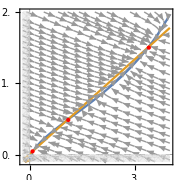

```mathematica
Only1Ind=NullclinePlotSystem[{dpdtOnly1Ind,dxdt},Append[params2d,<|"ρ"->0.07,"c"->6|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.002,0.04} ,{-100,2000}},FontStyle->"LaTeX",PlotSize->"Three",
Epilog->{{Red,PointSize@Medium,Point[{0.0008,45}]},{Red,PointSize@Medium,Point[{0.011,485}]},{Red,PointSize@Medium,Point[{0.034,1500}]}}]
```

```mathematica
dpdtOnly1Trans[p_,x_,params_]:=params[["ρ"]] (
ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]
)/(
1+
ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]
)-p;
```

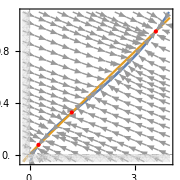

```mathematica
Only1Trans=NullclinePlotSystem[{dpdtOnly1Trans,dxdt},Append[params2d,<|"ρ"->0.13,"c"->3|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.002,0.04} ,{-55,1100}},FontStyle->"LaTeX",PlotSize->"Three",
Epilog->{{Red,PointSize@Medium,Point[{0.0025,75}]},{Red,PointSize@Medium,Point[{0.012,325}]},{Red,PointSize@Medium,Point[{0.036,950}]}}]
```

```mathematica
dpdtOnly1Both[p_,x_,params_]:=params[["ρ"]] (
ActiveXapROnly1Ind[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]
)/(
1+
ActiveXapROnly1Ind[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]
)-p;
```

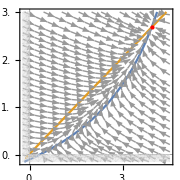

```mathematica
Only1Both=NullclinePlotSystem[{dpdtOnly1Both,dxdt},Append[params2d,<|"XapR"->5,"ρ"->0.1|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.00225,0.045} ,{-150,3000}},FontStyle->"LaTeX",PlotSize->"Three",
Epilog->{{Red,PointSize@Medium,Point[{0.0392,2680}]}}]
```

```mathematica
FewerSites=Graphics[{Inset[Only1Ind,ImageScaled[{0.01,0}],ImageScaled[{0,0}]],Inset[Only1Trans,ImageScaled[{0.34,0}],ImageScaled[{0,0}]],Inset[Only1Both,ImageScaled[{0.67,0}],ImageScaled[{0,0}]],
Inset[MaTeX["\\mathrm{(A)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],Inset[MaTeX["\\mathrm{(B)}",Magnification->1.2],ImageScaled[{0.33,1}],ImageScaled[{0,1}]],Inset[MaTeX["\\mathrm{(C)}",Magnification->1.2],ImageScaled[{0.66,1}],ImageScaled[{0,1}]]},PlotRange->{All,{-1,1}200/580},ImageSize->{580,Automatic}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","FewerSites.pdf"}],FewerSites];
```

```mathematica
FewerSitesresize=Show[ImportString[ExportString[FewerSites,"PDF"],"PDF"],ImageSize->5.2*inch];
```

```mathematica
Export[FileNameJoin[{"Exports","FewerSites.eps"}],FewerSitesresize];
```

#### Transcription Models

With basal & inactive state transcription rate:

```mathematica
dpdtRates[p_,x_,params_]:=params[["ρ"]] ((
ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]^2
Exp[params[["ϵ_coop"]]])+
(params[["r_I"]] 2 ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]])+
(params[["r_0"]] 1)
)/(
1+
2 ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]+
ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]^2
Exp[params[["ϵ_coop"]]]
)-p;
```

```mathematica
MoreRates=NullclinePlotSystem[{dpdtRates,dxdt},Append[params2d,<|"r_I"->10^(-2),"r_0"->10^(-3)|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.000475,0.0095} ,{-35,700}},FontStyle->"LaTeX",PlotSize->"Two"];
```

With different XapR dissociation constants:

```mathematica
dpdtConst[p_,x_,params_]:=params[["ρ"]] (
ActiveXapR[x,params[["XapR1"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]] ActiveXapR[x,params[["XapR2"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]
Exp[params[["ϵ_coop"]]]
)/(
1+
ActiveXapR[x,params[["XapR1"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]+
ActiveXapR[x,params[["XapR2"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]+
ActiveXapR[x,params[["XapR1"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]] ActiveXapR[x,params[["XapR2"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]
Exp[params[["ϵ_coop"]]]
)-p;
```

```mathematica
DifferentXapRConstants=NullclinePlotSystem[{dpdtConst,dxdt},Append[params2d,<|"XapR1"->0.1,"XapR2"->10,"c"->16|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.000475,0.0095} ,{-35,700}},FontStyle->"LaTeX",PlotSize->"Two"];
```

```mathematica
DifferentTranslation=Graphics[{Inset[MoreRates,ImageScaled[{0.01,0}],ImageScaled[{0,0}]],Inset[DifferentXapRConstants,ImageScaled[{1,0}],ImageScaled[{1,0}]],Inset[MaTeX["\\mathrm{(A)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],Inset[MaTeX["\\mathrm{(B)}",Magnification->1.2],ImageScaled[{0.525,1}],ImageScaled[{0,1}]]},
PlotRange->{All,{-1,1}280/540},ImageSize->{540,Automatic}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","FigSI1.pdf"}],DifferentTranslation];
```

## Stochastic Simulation

### Varying C

```mathematica
LowData=Import["PythonExport/Paper/Low.csv"][[7;;]][[;;,2]];
```

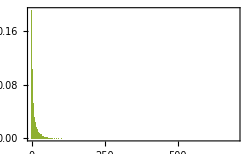

```mathematica
HistLow=Histogram[LowData,{1},"Probability",PlotRange->{{0,700},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->13.5],MaTeX["\\text{probability}","FontSize"->13.5]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,3]]
```

```mathematica
PhaseLow=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"c"->12|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.0005,0.01} ,{-45,900}},FontStyle->"LaTeX",PlotSize->"Three",PlotSize->"Three"];
```

```mathematica
BimodalData=Import["PythonExport/Paper/Bimodal.csv"][[7;;]][[;;,2]];
```

```mathematica
HistBimodal=Histogram[BimodalData,{1},"Probability",PlotRange->{{0,700},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->13.5],MaTeX["\\text{probability}","FontSize"->13.5]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,3]];
```

```mathematica
PhaseBimodal=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"c"->18.5|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.0005,0.01} ,{-45,900}},FontStyle->"LaTeX",PlotSize->"Three"];
```

```mathematica
HighData=Import["PythonExport/Paper/High.csv"][[7;;]][[;;,2]];
```

```mathematica
HistHigh=Histogram[HighData,{1},"Probability",PlotRange->{{0,700},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->13.5],MaTeX["\\text{probability}","FontSize"->13.5]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,3]];
```

```mathematica
PhaseHigh=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"c"->25|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.0005,0.01} ,{-45,900}},FontStyle->"LaTeX",PlotSize->"Three"];
```

```mathematica
HistogramsC=Graphics[{Inset[HistLow,ImageScaled[{0.01,0.84}],ImageScaled[{0,0.5}]],Inset[PhaseLow,ImageScaled[{1,0.84}],ImageScaled[{1,0.5}]],Inset[MaTeX["\\mathrm{(A)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],
Inset[HistBimodal,ImageScaled[{0.01,0.5025}],ImageScaled[{0,0.5}]],Inset[PhaseBimodal,ImageScaled[{1,0.5025}],ImageScaled[{1,0.5}]],Inset[MaTeX["\\mathrm{(B)}",Magnification->1.2],ImageScaled[{0,0.66525}],ImageScaled[{0,1}]],
Inset[HistHigh,ImageScaled[{0.01,0.165}],ImageScaled[{0,0.5}]],Inset[PhaseHigh,ImageScaled[{1,0.165}],ImageScaled[{1,0.5}]],Inset[MaTeX["\\mathrm{(C)}",Magnification->1.2],ImageScaled[{0,0.325}],ImageScaled[{0,1}]]},
PlotRange->{All,{-1,1} 1.315},ImageSize->{450,Automatic}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","HistogramsC.pdf"}],HistogramsC];
```

```mathematica
HistogramsCresize=Show[ImportString[ExportString[HistogramsC,"PDF"],"PDF"],ImageSize->5.2*inch];
```

```mathematica
Export[FileNameJoin[{"Exports","HistogramsC.eps"}],HistogramsCresize];
```

### Time Series and Adaptation Times

Stochastic Version:

```mathematica
TimeSeriesData=Import["PythonExport/Paper/TimeSeries.csv"];
```

```mathematica
ImageSize->350,BaseStyle->{FontFamily->"Times",FontSize->11}
```

```mathematica
StochasticTimeEvolution=ListLinePlot[Table[{#[[i,1]]/10^5,#[[i,2]]}&@TimeSeriesData,{i,1,Length[TimeSeriesData]}],Frame->True,FrameLabel->{MaTeX["\\mathrm{time \\ [10^5 \\ s]}","FontSize"->15],MaTeX["\\text{number of proteins}","FontSize"->15]},Evaluate@Join[plotOptionsBasic],ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->13}];(*,PlotLegends->Placed[LineLegend[{MaTeX["\\text{Stochastic Simulation}","FontSize"->14]}],Above]]*)
```

Deterministic Version:

```mathematica
DetSol=NDSolve[{p'[t]==dpdt[p[t],x[t],Append[params2d,"c"->25]],x'[t]==dxdt[p[t],x[t],Append[params2d,"c"->25]],p[0]==0,x[0]==0},{x,p},{t,0,250}];
```

```mathematica
DeterministicTimeEvolution=Plot[DetSol[[1,2,2]][t*(5 *10)]*5 10^4,{t,0,250/(5 10)},PlotRange->{{0,5},{0,700}},Frame->True,Evaluate@Join[plotOptionsBasic],ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->13},FrameLabel->{MaTeX["\\mathrm{time \\ [10^5 \\ s]}","FontSize"->15],MaTeX["\\text{number of proteins}","FontSize"->15]},PlotStyle->ColorData[97,2]];(*,PlotLegends->Placed[LineLegend[{MaTeX["\\text{Deterministic Solution}","FontSize"->14]}],Above]];*)
```

Putting together:

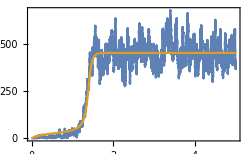

```mathematica
TimeEvolution=Show[StochasticTimeEvolution,DeterministicTimeEvolution]
```

```mathematica
AdaptationTimesData=Flatten[Import["PythonExport/Paper/AdaptationTimes.csv"][[7;;]]];
```

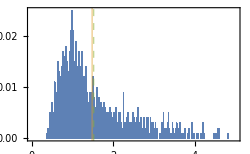

```mathematica
AdaptationTimes=Histogram[AdaptationTimesData/10^5,200,"Probability",PlotRange->{{0,5},All},Frame->True,Evaluate@Join[plotOptionsBasic],FrameLabel->{MaTeX["\\text{time to steady-state mean } \\mathrm{[10^5 \\ s]}","FontSize"->15],MaTeX["\\text{probability}","FontSize"->15]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->13},ChartStyle->ColorData[97,1],GridLines->{{{1.48,Directive[ColorData[97,2],Thick,Opacity[1]]},{Mean[AdaptationTimesData]/10^5,Directive[ColorData[97,3],Thick,Dashed,Opacity[1]]}},{}},GridLinesStyle->{{{Directive[ColorData[97,2],Thick],Directive[ColorData[97,3],Thick,Dashed]}}}]
```

```mathematica
TimePlots=Graphics[{Inset[TimeEvolution,ImageScaled[{0.01,0}],ImageScaled[{0,0}]],Inset[AdaptationTimes,ImageScaled[{1,0}],ImageScaled[{1,0}]],Inset[MaTeX["\\mathrm{(A)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],Inset[MaTeX["\\mathrm{(B)}",Magnification->1.2],ImageScaled[{0.525,1}],ImageScaled[{0,1}]]},PlotRange->{All,{-1,1}195/540},ImageSize->{540,Automatic}]
```

-Graphics-

```mathematica
TimePlotLegended=Legended[TimePlots,Placed[LineLegend[{ColorData[97,1],ColorData[97,2],{Dashed,ColorData[97,3]}},MaTeX[#,"FontSize"->15]&/@{"\\text{Stochastic}","\\text{Deterministic}","\\text{Mean of stochastic distribution}"},LegendLayout->{"Row",1},Spacings->{0.5,2.5,-1},LegendMarkerSize->30,LegendMargins->-3],Below]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","TimeEvolution.pdf"}],TimePlotLegended];
```

```mathematica
TimeEvolutionresize=Show[ImportString[ExportString[TimePlotLegended,"PDF"],"PDF"],ImageSize->5.2*inch];
```

```mathematica
Export[FileNameJoin[{"Exports","TimeEvolution.eps"}],TimeEvolutionresize];
```

### Hysteresis

```mathematica
Hyst1Data=Import["PythonExport/Hysteresis1.csv"][[7;;]][[;;,2]];
```

Import::nffil: File not found during Import.

Part::take: Cannot take positions 7 through -1 in $Failed.

Part::partd: Part specification $Failed⟦7;;All⟧⟦1;;All,2⟧ is longer than depth of object.

```mathematica
HistHyst1=Histogram[Hyst1Data,{1},"Probability",PlotRange->{{0,650},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,1]];
```

Histogram::ldata: $Failed⟦7;;All⟧⟦1;;All,2⟧ is not a valid dataset or list of datasets.

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

```mathematica
PhaseHyst1=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"c"->12|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.0005,0.01} ,{-35,700}},FontStyle->"LaTeX",PlotSize->"Three"];
```

```mathematica
Hyst2Data=Import["PythonExport/Hysteresis2.csv"][[7;;]][[;;,2]];
```

Import::nffil: File not found during Import.

Part::take: Cannot take positions 7 through -1 in $Failed.

Part::partd: Part specification $Failed⟦7;;All⟧⟦1;;All,2⟧ is longer than depth of object.

```mathematica
HistHyst2=Histogram[Hyst2Data,{1},"Probability",PlotRange->{{0,650},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,1]];
```

Histogram::ldata: $Failed⟦7;;All⟧⟦1;;All,2⟧ is not a valid dataset or list of datasets.

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

```mathematica
PhaseHyst2=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"c"->10|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.0005,0.01} ,{-35,700}},FontStyle->"LaTeX",PlotSize->"Three"];
```

```mathematica
Hyst3Data=Import["PythonExport/Hysteresis3.csv"][[7;;]][[;;,2]];
```

Import::nffil: File not found during Import.

Part::take: Cannot take positions 7 through -1 in $Failed.

Part::partd: Part specification $Failed⟦7;;All⟧⟦1;;All,2⟧ is longer than depth of object.

```mathematica
HistHyst3=Histogram[Hyst3Data,{1},"Probability",PlotRange->{{0,650},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,1]];
```

Histogram::ldata: $Failed⟦7;;All⟧⟦1;;All,2⟧ is not a valid dataset or list of datasets.

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

```mathematica
PhaseHyst3=NullclinePlotSystem[{dpdt,dxdt},Append[params2d,<|"c"->9|>],FrameLabel->{"\\mathrm{[p]_a}","\\mathrm{[x]_a}"},PlotRange->{{-0.0005,0.01} ,{-35,700}},FontStyle->"LaTeX",PlotSize->"Three"];
```

```mathematica
HysteresisC=Graphics[{Inset[HistHyst1,ImageScaled[{0.01,0.84}],ImageScaled[{0,0.5}]],Inset[PhaseHyst1,ImageScaled[{1,0.84}],ImageScaled[{1,0.5}]],Inset[MaTeX["\\mathrm{(A)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],
Inset[HistHyst2,ImageScaled[{0.01,0.5025}],ImageScaled[{0,0.5}]],Inset[PhaseHyst2,ImageScaled[{1,0.5025}],ImageScaled[{1,0.5}]],Inset[MaTeX["\\mathrm{(B)}",Magnification->1.2],ImageScaled[{0,0.66525}],ImageScaled[{0,1}]],
Inset[HistHyst3,ImageScaled[{0.01,0.165}],ImageScaled[{0,0.5}]],Inset[PhaseHyst3,ImageScaled[{1,0.165}],ImageScaled[{1,0.5}]],Inset[MaTeX["\\mathrm{(C)}",Magnification->1.2],ImageScaled[{0,0.325}],ImageScaled[{0,1}]]},
PlotRange->{All,{-1,1} 1.315},ImageSize->{450,Automatic}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","FigSI8.pdf"}],HysteresisC];
```

### Including Bursts

```mathematica
BurstSeries1Data=Import["PythonExport/Paper/BurstsEvolution1.csv"];
```

```mathematica
BurstEvolution1=ListLinePlot[Table[{#[[i,1]]/10^5,#[[i,2]]}&@BurstSeries1Data,{i,1,Length[BurstSeries1Data]}],Frame->True,FrameLabel->{MaTeX["\\mathrm{time \\ [10^5 \\ s]}","FontSize"->14],MaTeX["\\text{number of proteins}","FontSize"->14]},Evaluate@Join[plotOptionsBasic],ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->13}];
```

```mathematica
BurstSeries2Data=Import["PythonExport/Paper/BurstsEvolution2.csv"];
```

```mathematica
BurstEvolution2=ListLinePlot[Table[{#[[i,1]]/10^5,#[[i,2]]}&@BurstSeries2Data,{i,1,Length[BurstSeries2Data]}],Frame->True,FrameLabel->{MaTeX["\\mathrm{time \\ [10^5 \\ s]}","FontSize"->14],MaTeX["\\text{number of proteins}","FontSize"->14]},Evaluate@Join[plotOptionsBasic],ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->13}];
```

```mathematica
BurstsAdaptationTimesData=Flatten[Import["PythonExport/Paper/BurstsAdaptationTimes.csv"][[7;;]]];
```

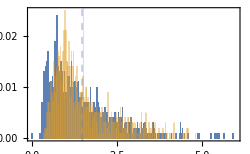

```mathematica
BurstsAdaptationTimes=Show[Histogram[BurstsAdaptationTimesData/10^5,400,"Probability",PlotRange->{{0,6},All},Frame->True,Evaluate@Join[plotOptionsBasic],FrameLabel->{MaTeX["\\text{time to steady-state mean } \\mathrm{[10^5 \\ s]}","FontSize"->15],MaTeX["\\text{probability}","FontSize"->15]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->13},ChartStyle->ColorData[97,1],GridLines->{{{Mean[BurstsAdaptationTimesData]/10^5,Directive[ColorData[97,1],Thick,Dashed,Opacity[1]]},{Mean[AdaptationTimesData]/10^5,Directive[ColorData[97,2],Thick,Opacity[0.5]]}},{}}],
Histogram[AdaptationTimesData/10^5,200,"Probability",PlotRange->{{0,6},All},Frame->True,Evaluate@Join[plotOptionsBasic],FrameLabel->{MaTeX["\\text{time to steady-state mean } \\mathrm{[10^5 \\ s]}","FontSize"->15],MaTeX["\\text{probability}","FontSize"->15]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->13},ChartStyle->{{ColorData[97,2]},{Opacity[0.4]}}]]
```

```mathematica
BurstsEvolution=Graphics[{Inset[BurstEvolution1,ImageScaled[{0.01,0}],ImageScaled[{0,0}]],Inset[BurstsAdaptationTimes,ImageScaled[{1,0}],ImageScaled[{1,0}]],Inset[MaTeX["\\mathrm{(A)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],Inset[MaTeX["\\mathrm{(B)}",Magnification->1.2],ImageScaled[{0.525,1}],ImageScaled[{0,1}]]},PlotRange->{All,{-1,1}195/540},ImageSize->{540,Automatic}]
```

-Graphics-

```mathematica
BurstsEvolutionLegended=Legended[BurstsEvolution,Placed[LineLegend[{ColorData[97,1],ColorData[97,2]},MaTeX[#,"FontSize"->14]&/@{"\\text{With bursting}","\\text{Without bursting}"},LegendLayout->{"Row",1},Spacings->{1,4,-1},LegendMarkerSize->30,LegendMargins->-3],Below]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","FigSI6_7.pdf"}],BurstsEvolutionLegended];
```

```mathematica
BurstsEvolutionresize=Show[ImportString[ExportString[BurstsEvolutionLegended,"PDF"],"PDF"],ImageSize->5.2*inch];
```

```mathematica
Export[FileNameJoin[{"Exports","FigSI6_7.eps"}],BurstsEvolutionresize];
```

```mathematica
BurstDistData1=Import["PythonExport/Paper/BurstsDistribution1.csv"][[7;;]][[;;,2]];
BurstDistribution1=Histogram[BurstDistData1,{3},"Probability",PlotRange->{{0,850},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,1]];
Dist1=Show[BurstDistribution1,Histogram[LowData,{3},"Probability",PlotRange->{{0,850},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->{{Opacity[0.4]},{ColorData[97,2]}}]];
```

```mathematica
BurstDistData2=Import["PythonExport/Paper/BurstsDistribution2.csv"][[7;;]][[;;,2]];
BurstDistribution2=Histogram[BurstDistData2,{3},"Probability",PlotRange->{{0,850},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,1]];
```

```mathematica
BurstDistData3=Import["PythonExport/Paper/BurstsDistribution3.csv"][[7;;]][[;;,2]];
BurstDistribution3=Histogram[BurstDistData3,{3},"Probability",PlotRange->{{0,850},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,1]];
Dist3=Show[BurstDistribution3,Histogram[BimodalData,{3},"Probability",PlotRange->{{0,850},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->{{Opacity[0.4]},{ColorData[97,2]}}]];
```

```mathematica
BurstDistData4=Import["PythonExport/Paper/BurstsDistribution4.csv"][[7;;]][[;;,2]];
BurstDistribution4=Histogram[BurstDistData4,{3},"Probability",PlotRange->{{0,850},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->ColorData[97,1]];
Dist4=Show[BurstDistribution4,Histogram[HighData,{3},"Probability",PlotRange->{{0,850},All},Frame->True,FrameLabel->{MaTeX["\\text{number of proteins}","FontSize"->14],MaTeX["\\text{probability}","FontSize"->14]},ImageSize->250,BaseStyle->{FontFamily->"Times",FontSize->11},ChartStyle->{{Opacity[0.4]},{ColorData[97,2]}}]];
```

```mathematica
BurstsDistributionsAB=Graphics[{Inset[Dist1,ImageScaled[{0.01,0}],ImageScaled[{0,0}]],Inset[BurstDistribution2,ImageScaled[{1,0}],ImageScaled[{1,0}]],Inset[MaTeX["\\mathrm{(A)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],Inset[MaTeX["\\mathrm{(B)}",Magnification->1.2],ImageScaled[{0.525,1}],ImageScaled[{0,1}]]},PlotRange->{All,{-1,1}190/540},ImageSize->{540,Automatic}];
```

```mathematica
BurstsDistributionsCD=Graphics[{Inset[Dist3,ImageScaled[{0.01,0}],ImageScaled[{0,0}]],Inset[Dist4,ImageScaled[{1,0}],ImageScaled[{1,0}]],Inset[MaTeX["\\mathrm{(C)}",Magnification->1.2],ImageScaled[{0,1}],ImageScaled[{0,1}]],Inset[MaTeX["\\mathrm{(D)}",Magnification->1.2],ImageScaled[{0.525,1}],ImageScaled[{0,1}]]},PlotRange->{All,{-1,1}190/540},ImageSize->{540,Automatic}];
```

```mathematica
BurstsDistributions=Graphics[{Inset[BurstsDistributionsAB,ImageScaled[{0.01,1}],ImageScaled[{0,1}]],Inset[BurstsDistributionsCD,ImageScaled[{0.01,0}],ImageScaled[{0,0}]]},PlotRange->{All,{-1,1}390/550},ImageSize->{550,Automatic}]
```

-Graphics-

```mathematica
BurstsDistributionsLegended=Legended[BurstsDistributions,Placed[LineLegend[{ColorData[97,1],ColorData[97,2]},MaTeX[#,"FontSize"->14]&/@{"\\text{With bursting}","\\text{Without bursting}"},LegendLayout->{"Row",1},Spacings->{1,4,-1},LegendMarkerSize->30,LegendMargins->1],Below]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{"Exports","FigSI6_7_2.pdf"}],BurstsDistributionsLegended];
```

```mathematica
BurstsDistributionsresize=Show[ImportString[ExportString[BurstsDistributionsLegended,"PDF"],"PDF"],ImageSize->5.2*inch];
```

```mathematica
Export[FileNameJoin[{"Exports","FigSI6_7_2.eps"}],BurstsDistributionsresize];
```